# Euler 243: Resilient Fractions

## Helpers:

```mathematica
Clear[R]
threshold =15499/94744;
primeFactors[n_]:=First/@FactorInteger[n]
p=Table[∏_n^m Prime[n],{m,10}]
```

{2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

## The Solution:

No... I don’t entirely understand it yet. I still can’t come up with a EulerPhi function that remotely competes with Mathematica.

```mathematica
My`EulerPhi[n_]:=n ∏_m^primeFactors[n] (1-1/m)
R[n_]:=R[n]=(My`EulerPhi[n])/(n-1)
search[min_,max_]:=Select[Range[min,max,min],R[#]<threshold&,1]
Timing[search[p[[9]],p[[10]]]//First]
```

{0.000512,892371480}

```mathematica
Monitor[Table[Timing[search[p[[m]],p[[10]]]//First],{m,7,9}],k]//TableForm
```

0.139712 | 892371480
0.000527 | 892371480
0.000033 | 892371480

## Other Visualizations:

```mathematica
Table[{n, R[n]},{n,Take[p,8]}]//TableForm
```

2 | 1
6 | 2/5
30 | 8/29
210 | 48/209
2310 | 480/2309
30030 | 5760/30029
510510 | 92160/510509
9699690 | 1658880/9699689

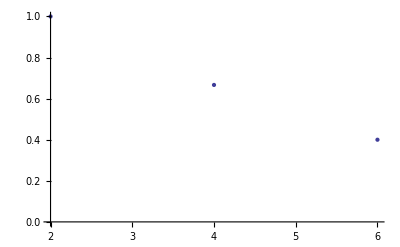
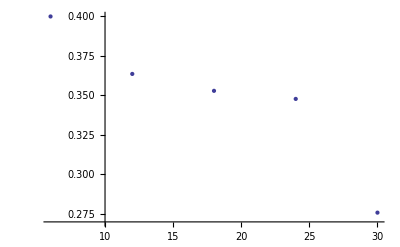
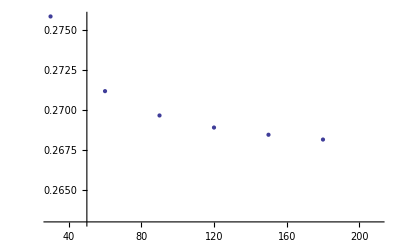
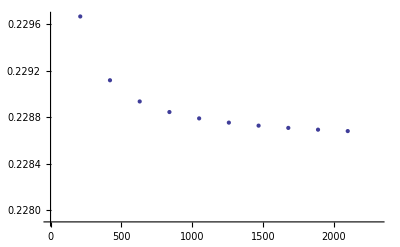
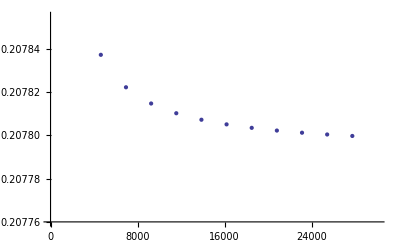
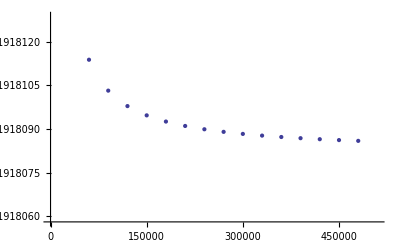
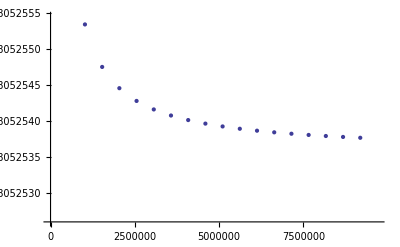
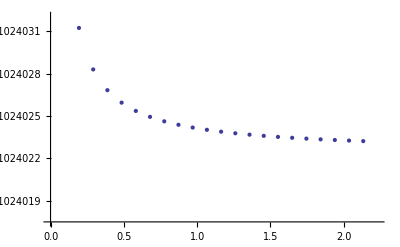

```mathematica
Monitor[Table[ListPlot[Table[{m,R[m]},{m,p[[q]],p[[q+1]],p[[q]]}]],{q,1,9}],q]
```